7.83619×10^-16

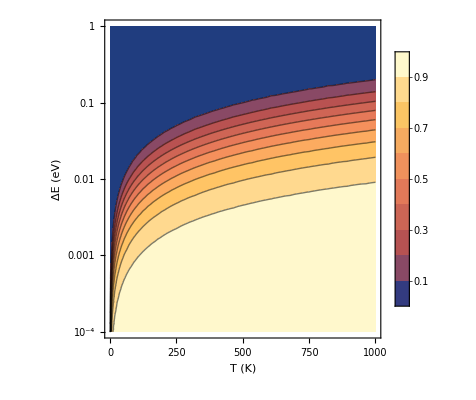

```mathematica
Clear["`*"]

g2=g1;
k=1.380*10^-23;(*Joule per Kelvin https://en.wikipedia.org/wiki/Boltzmann_constant#Value_in_different_units*)

N2N1=(g2/g1)Exp[-dE*(1.6*10^-19)/(k T)];

N2N1/.{dE->3*10^0,T->1000}
ContourPlot[N2N1,{T,0,1000},{dE,1*10^-4, 1}, PlotLegends->Automatic, ScalingFunctions->{None,"Log"}, FrameLabel->{"T (K)","ΔE (eV)"}]
```